# Gravitational Wave Constraints on the Progenitors of Fast Radio Bursts

## Tom Callister thomas.a.callister@gmail.com March 2016

This notebook contains code used to produce the values and plots shown in “Gravitational Wave Constraints on the Progenitors of Fast Radio Bursts.”

Sect. 1: Constants & Front Matter
*Must* run. Defines notebook directory and physical constants.

Sect. 2: Compute Fiducial Distances
Imports data from the file “frbcat_2016-03-12.txt,” downloaded on March 12, 2016 from the FRB Catalogue hosted at:
http://www.astronomy.swin.edu.au/pulsar/frbcat/
Note that the original data file from the FRB catalogue has been edited to include only one entry per unique FRB.
Converts dispersion measures to FRB distance estimates and creates histogram seen in Fig. 1.

Sect. 3: 
*Must* run to run Sects. 4 and 5.
Defines the various rate estimates (both from pop synth and LIGO/Virgo experiments) used in the paper.
Data sourced from:
- B. P. Abbott et al, Living Rev. Relativ. 19, (2016).
- J. Abadie et al, Class. Quantum Gravity 27, 173001 (2010).
- B. P. Abbott, Phys. Rev. Lett. 116, 061102 (2016).

Sect. 4:
Computes the FRB fractions quoted in the paper.

Sect. 5:
Run to create Fig. 2, which compares CBC and FRB rate densities

## 1. Constants & Front Matter

```mathematica
(* Set directory, misc notebook preferences *)
SetDirectory[NotebookDirectory[]];
colors=ColorData[97,"ColorList"];
Needs["ErrorBarPlots`"]

(* Physical constants, all SI units *)
h=0.67;
H0=(100h*10^3)/(10^6 pc) (* Hubble constant *);
G=6.67*10^-11 (* Newton's constant *);
c = 2.998*10^8 (* Speed of light *);
pc = 3.086*10^16 (* Parsec *);
Mpc = 10^6 pc (* Megaparsec *);
mp=1.67*10^-27(* Proton mass *);

(* Planck 2015 energy densities *)
Ωm=0.31 (* Matter *);
ΩΛ=0.69 (* Dark energy *);
Ωb=0.022/h^2 (* Baryons *);
```

```mathematica
(* Free electron density *)
(((3 H0^2)/(8π G))Ωb)/mp(1/100)^3
```

2.47554×10^-7

## 2. Compute Fidicual Distances

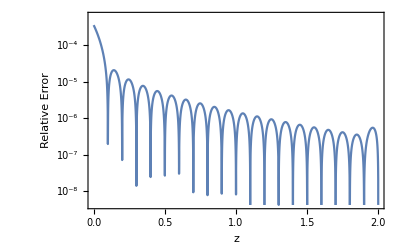

```mathematica
(* Import dispersion measure data *)
data=Import["frbcat_2016-03-12.txt","Data"]⟦2;;⟧;
DMs=Transpose[data]⟦19⟧ (* Dispersion Measures *);
δDMs=Transpose[data]⟦20⟧ (* Dispersion measure errors *);

(* Dispersion Measure *)
(* Factors of (1/pc) and (1/100) convert to SI units *)
DM[z_?NumericQ]:=(1/pc)(1/100)^3(3c H0 Ωb)/(8π G mp)NIntegrate[(1+zz)/(√(Ωm(1+zz)^3+ΩΛ)),{zz,0,z}]

(* Proper Distance *)
r[z_?NumericQ]:=c/H0 NIntegrate[1/(√(ΩΛ+Ωm(1+zz)^3)),{zz,0,z}] 

(* Create interpolation function *)
zFromD=Interpolation[Table[{r[z],z},{z,0,2,0.1}]];

(* Sanity check interpolation function *)
LogPlot[Abs[(z-zFromD[r[z]])/z],{z,0,2},
Frame->True,
FrameLabel->{"z","Relative Error"},
GridLines->Automatic]
```

```mathematica
(* Initialize arrays *)
Dists=Table[0,{i,1,Length[DMs]}];
zs=Table[0,{i,1,Length[DMs]}];

(* For each FRB, compute redshift and distance *)
For[i=1,i≤Length[DMs],i++,
zFRB=Quiet[z/.NSolve[DMs⟦i⟧==DM[z],z]⟦1⟧];
zs⟦i⟧=zFRB;
Dists⟦i⟧=r[zFRB]/(10^9 pc);
]

(* Print median, mean distance *)
Median[Dists]
Mean[Dists]
```

2.41305

2.39168

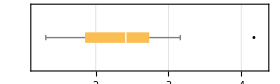

```mathematica
(* Box & whisker plot of distances *)
(* Box denotes 25% and 75% quantiles, whiskers denote full distribution except for outlier *)
bwPlot=BoxWhiskerChart[Dists,{"Outliers"},
ImageSize->{280,130},
AspectRatio->0.3,
Frame->True,
FrameLabel->{"D (Gpc)"},
GridLines->{Automatic,None},
BarOrigin->Left
]
```

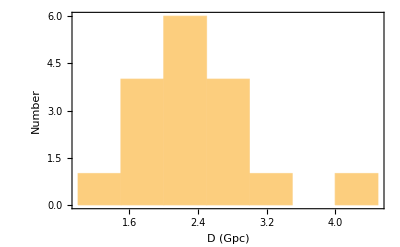

```mathematica
(* Histogram of distances *)
hist=Histogram[Dists,{0.5},
Frame->True,
FrameLabel->{Style["D (Gpc)",11],Style["Number",11],Style["Redshift",11],},
FrameTicks->{
{Automatic,Automatic},
{Automatic,Table[{r[z]/(10^9 pc),z},{z,.25,1.5,.25}]}
},
FrameTicksStyle->10
(*Epilog->{Thickness[0.009],Gray,Line[{{3,0},{3,6.25}}]}*)]
Export["DistHistogram.pdf",hist];
```

## 3. Experimental/Fiducial Values

```mathematica
(* Fiducial FRB rates *)
(* d = Distance in Gpc *)
(* Ω = Solid angle of emission in Sr *)
(* R = Observed rate in units #/day *)
dRdVobs[d_,Ω_,R_]:=(R*365.)/((4π)/3 d^3)((4π)/Ω) (* Number/Gpc^3/yr *);
dRdVobs[3,4π,10^4]
dRdVobs[3,4π,2500]
```

32273.1

8068.27

```mathematica
(* Projected aLIGO horizons in Gpc *)
(* O1: 40-80 Mpc BNS range *)
(* O2: 80-120 Mpc *)
(* O3: 120-170 Mpc *)
(* Note that we take the NSBH range to be approximately 1.6 times the BNS range, following Abbot et al, LRR 19 (2016) *)

(* Observing scenario avg. search range O1 *)
RbnsO1=(Integrate[R^3,{R,40,80}]/(80-40.))^(1/3)*10^-3 (* Gpc *);
RnsbhO1=1.6*RbnsO1;

(* Observing scenario avg. search range O2 *)
RbnsO2=(Integrate[R^3,{R,80,120}]/(120-80.))^(1/3)*10^-3 (* Gpc *);
RnsbhO2=1.6*RbnsO2;

(* Observing scenario avg. search range O3 *)
RbnsO3=(Integrate[R^3,{R,120,170}]/(170-120.))^(1/3)*10^-3 (* Gpc *);
RnsbhO3=1.6*RbnsO3;
```

```mathematica
(* Pop synth and pulsar bounds, Number/Gpc^3/yr *)
dRdVbnsLow=(0.01)*10^3;
dRdVbnsHigh=(10)*10^3;
dRdVnsbhLow=(.0006)*10^3;
dRdVnsbhHigh=(1.)*10^3;

(* GW150914, Number/Gpc^3/yr *)
dRdVbbhLow=2.;
dRdVbbhHigh=400.;

(* S6VSR23 Limits *)
dRdVnsbhS6=3.1*10^-5*10^9(* Number/Gpc^3/yr *);
dRdVbnsS6=1.3*10^-4*10^9 (* Number/Gpc^3/yr *);

(* O1 Limits *)
(* Note: Rate density limits given by 1/(Observing volume)*(Observing time) *)
(* 4 month run *)
dRdVbnsO1=1/((4π)/3(RbnsO1)^3(4/12.)) (* Number/Gpc^3/yr *);
dRdVnsbhO1=1/((4π)/3(RnsbhO1)^3(4/12.)) (* Number/Gpc^3/yr *);

(* O2 Limits *)
(* 6 month run *)
dRdVbnsO2=1/((4π)/3(RbnsO2)^3(6/12.)) (* Number/Gpc^3/yr *);
dRdVnsbhO2=1/((4π)/3(RnsbhO2)^3(6/12.)) (* Number/Gpc^3/yr *);

(* O3 Limits *)
(* 9 month run *)
dRdVbnsO3=1/((4π)/3(RbnsO3)^3(9/12.)) (* Number/Gpc^3/yr *);
dRdVnsbhO3=1/((4π)/3(RnsbhO3)^3(9/12.)) (* Number/Gpc^3/yr *);
```

## 4. Fractions Quoted in Paper

```mathematica
(* Low beaming solid angle *)
Ωlow=Integrate[Sin[θ],{ϕ,0,2π},{θ,0,π/4}]//N
```

1.8403

### BNS Progenitor Fractions

```mathematica
(* BNS Pop Synthesis *)
ηbnsLow=dRdVbnsLow/dRdVobs[3,4π,2500] (* Low estimate, isotropic beaming *)
ηbnsHigh=dRdVbnsHigh/dRdVobs[3,4π,2500] (* High estimate, isotropic beaming *)
ηbnsHigh=dRdVbnsHigh/dRdVobs[3,Ωlow,2500] (* High estimate, beamed *)
```

0.00123942

1.23942

0.181509

```mathematica
(* BNS O1 *)
dRdVbnsO1/dRdVobs[3,4π,2500] (* Isotropic beaming *)
dRdVbnsO1/dRdVobs[3,Ωlow,2500](* Low beaming *)
```

0.369863

0.0541652

### NSBH Progenitor Fractions

```mathematica
(* NSBH Pop Synthesis *)
ηnsbhLow=dRdVnsbhLow/dRdVobs[3,4π,2500] (* Low estimate, isotropic *)
ηnsbhHigh=dRdVnsbhHigh/dRdVobs[3,4π,2500] (* High estimate, isotropic *)
```

0.0000743654

0.123942

```mathematica
(* NSBH LIGO search results *)
dRdVnsbhS6/dRdVobs[3,4π,2500] (* S6 *)
dRdVnsbhO1/dRdVobs[3,4π,2500] (* O1 *)
dRdVnsbhO1/dRdVobs[3,Ωlow,2500] (* O2 *)
```

3.84221

0.0902986

0.0132239

### BBH Progenitor Fractions

```mathematica
(* BBH Fraction *)
dRdVbbhHigh/dRdVobs[3,4π,2500] (* Isotropic *)
dRdVbbhHigh/dRdVobs[3,Ωlow,2500] (* Beamed *)
```

0.0495769

0.00726037

## 5. Rate Plot

```mathematica
(* Manually specify plot bounds *)
ymin=10^-1;
ymax=10^6;

(* Compute range, FRB rates *)
range=Log10[ymax]-Log10[ymin] (* Do not change!! *);
RFRBmin=Robs[3,4π,2.5*10^3];
RFRBmax=Robs[3,4π,10^4];

(* Plot BNS bounds *)
bnsPoints=ListLogPlot[
{
{.2,dRdVbnsS6},
{.2,dRdVbnsO1},
{.2,dRdVbnsO2},
{.2,dRdVbnsO3}},
PlotMarkers->"-",
Frame->True,
GridLines->{None,Automatic},
GridLinesStyle->Directive[Gray,Thickness[3]],
PlotRange->{{0,1},{ymin,ymax}},
AxesOrigin->{0.,10^-7},
FrameLabel->{,Style["Rate (Gpc^-3yr^-1)",11]},
FrameTicks->{{Automatic,None},None},
FrameTicksStyle->10,
Prolog->{LightGray,Rectangle[Scaled[{0,(Log10[RFRBmin]-Log10[ymin])/range}],Scaled[{1,(Log10[RFRBmax]-Log10[ymin])/range}]]}
];

(* Plot NSBH bounds *)
nsbhPoints=ListLogPlot[
{
{.5,dRdVnsbhS6},
{.5,dRdVnsbhO1},
{.5,dRdVnsbhO2},
{.5,dRdVnsbhO3}},
PlotMarkers->"-",
PlotStyle->colors⟦2⟧
];

(* Draw bars *)
bnsBar=Graphics[{colors⟦1⟧,Rectangle[Scaled[{.1,(Log10[RbnsLow]-Log10[ymin])/range}],Scaled[{.15,(Log10[RbnsHigh]-Log10[ymin])/range}]]}];
bbhBar=Graphics[{colors⟦4⟧,Rectangle[Scaled[{.7,(Log10[RbbhLow]-Log10[ymin])/range}],Scaled[{.75,(Log10[RbbhHigh]-Log10[ymin])/range}]]}];
nsbhBar=Graphics[{colors⟦2⟧,Rectangle[Scaled[{.4,(Log10[RnsbhLow]-Log10[ymin])/range}],Scaled[{.45,(Log10[RnsbhHigh]-Log10[ymin])/range}]]}];

(* Build plot, add labels *)
FracPlot3Gpc=Show[
bnsPoints,nsbhPoints,bnsBar,bbhBar,nsbhBar,
Graphics[{colors⟦1⟧,Text["Predicted\nBNS Rate",Scaled[{0.26,0.28}],TextAlignment->Left]}],
Graphics[{colors⟦1⟧,
Text["S6VSR23",Scaled[{0.30,0.87}]],
Text["O1",Scaled[{0.25,0.64}]],
Text["O2",Scaled[{0.25,0.52}]],
Text["O3",Scaled[{0.25,0.43}]]}],
Graphics[{colors⟦2⟧,Text["Predicted\nNSBH Rate",Scaled[{0.57,0.15}],TextAlignment->Left]}],
Graphics[{colors⟦2⟧,
Text["S6VSR23",Scaled[{0.60,0.78}]],
Text["O1",Scaled[{0.55,0.55}]],
Text["O2",Scaled[{0.55,0.43}]],
Text["O3",Scaled[{0.55,0.33}]]}],
Graphics[{colors⟦4⟧,Text["Measured\nBBH Rate",Scaled[{0.86,0.25}],TextAlignment->Left]}],
Graphics[{Gray,Text["FRB Rate",Scaled[{0.85,0.82}],TextAlignment->Left]}]
]

Export["RateComparison_3.0Gpc.pdf",FracPlot3Gpc];
```

-Graphics-